```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,8000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

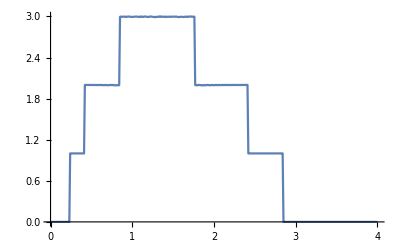

```mathematica
ListLinePlot[Table[{ω,tr[ω,0.0001,1,0]},{ω,0,4,0.01}]]
```

```mathematica
pris=Table[{ω,tr[ω,0.0001,1,0]},{ω,0,4,0.01}]
```

{{0.,2.8×10^-7},{0.01,2.8081×10^-7},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},{0.09,3.61694×10^-7},{0.1,3.86954×10^-7},{0.11,4.18578×10^-7},{0.12,4.58598×10^-7},{0.13,5.10023×10^-7},{0.14,5.77474×10^-7},{0.15,6.68349×10^-7},{0.16,7.95126×10^-7},{0.17,9.803×10^-7},{0.18,1.26801×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92698×10^-6},{0.22,0.0000129427},{0.23,0.000120119},{0.24,0.999916},{0.25,0.999991},{0.26,0.999998},{0.27,1.},{0.28,0.999998},{0.29,0.999999},{0.3,0.999999},{0.31,0.999946},{0.32,0.999915},{0.33,0.999952},{0.34,0.999996},{0.35,0.999822},{0.36,0.999769},{0.37,0.999735},{0.38,1.},{0.39,0.999893},{0.4,0.99963},{0.41,1.00011},{0.42,1.99987},{0.43,1.99945},{0.44,1.99999},{0.45,1.99952},{0.46,1.99971},{0.47,1.99943},{0.48,1.99973},{0.49,1.99925},{0.5,1.99995},{0.51,1.99998},{0.52,1.99872},{0.53,1.99903},{0.54,1.99915},{0.55,1.99899},{0.56,1.99923},{0.57,1.99871},{0.58,1.9985},{0.59,1.99935},{0.6,1.9983},{0.61,1.99973},{0.62,1.99964},{0.63,1.99728},{0.64,1.99869},{0.65,1.99639},{0.66,1.99654},{0.67,1.99915},{0.68,1.99865},{0.69,1.99668},{0.7,1.99573},{0.71,1.99501},{0.72,1.99995},{0.73,1.99796},{0.74,1.99942},{0.75,1.99859},{0.76,1.99888},{0.77,1.99973},{0.78,1.99422},{0.79,1.99392},{0.8,1.99748},{0.81,1.99466},{0.82,1.99673},{0.83,1.99427},{0.84,1.99729},{0.85,2.99415},{0.86,2.99738},{0.87,2.9969},{0.88,2.99368},{0.89,2.99688},{0.9,2.99703},{0.91,2.99826},{0.92,2.99306},{0.93,2.99479},{0.94,2.99702},{0.95,2.99795},{0.96,2.99838},{0.97,2.99731},{0.98,2.99533},{0.99,2.99384},{1.,2.99292},{1.01,2.99364},{1.02,2.99578},{1.03,2.99662},{1.04,2.99781},{1.05,2.99861},{1.06,2.99696},{1.07,2.99589},{1.08,2.99219},{1.09,2.9932},{1.1,2.99975},{1.11,2.99456},{1.12,2.99765},{1.13,2.99223},{1.14,2.99549},{1.15,2.99935},{1.16,2.99916},{1.17,2.99604},{1.18,2.99491},{1.19,2.99388},{1.2,2.99225},{1.21,2.99619},{1.22,2.99985},{1.23,2.99859},{1.24,2.99607},{1.25,2.99439},{1.26,2.99278},{1.27,2.99171},{1.28,2.99009},{1.29,2.99517},{1.3,2.99131},{1.31,2.99452},{1.32,2.99871},{1.33,2.99407},{1.34,2.99995},{1.35,2.99374},{1.36,2.99898},{1.37,2.99554},{1.38,2.99573},{1.39,2.99695},{1.4,2.991},{1.41,2.99716},{1.42,2.99663},{1.43,2.99259},{1.44,2.99574},{1.45,2.99645},{1.46,2.99659},{1.47,2.99298},{1.48,2.99688},{1.49,2.99598},{1.5,2.99759},{1.51,2.99686},{1.52,2.99775},{1.53,2.99612},{1.54,2.99757},{1.55,2.99537},{1.56,2.99078},{1.57,2.99069},{1.58,2.99396},{1.59,2.99454},{1.6,2.99467},{1.61,2.99472},{1.62,2.9927},{1.63,2.9921},{1.64,2.99471},{1.65,2.99782},{1.66,2.99345},{1.67,2.99714},{1.68,2.9918},{1.69,2.99801},{1.7,2.99855},{1.71,2.9991},{1.72,2.9991},{1.73,2.99487},{1.74,2.9974},{1.75,2.99466},{1.76,2.99766},{1.77,1.99834},{1.78,1.99608},{1.79,1.99395},{1.8,1.99764},{1.81,1.99978},{1.82,1.99923},{1.83,1.99669},{1.84,1.99756},{1.85,1.99419},{1.86,1.99449},{1.87,1.99911},{1.88,1.99467},{1.89,1.99628},{1.9,1.99475},{1.91,1.99973},{1.92,1.99872},{1.93,1.99955},{1.94,1.99567},{1.95,1.99658},{1.96,1.99597},{1.97,1.99901},{1.98,1.99937},{1.99,1.99601},{2.,1.9979},{2.01,1.99629},{2.02,1.99987},{2.03,1.99932},{2.04,1.99719},{2.05,1.99723},{2.06,1.99969},{2.07,1.99981},{2.08,1.99704},{2.09,1.9971},{2.1,1.99995},{2.11,1.99965},{2.12,1.99871},{2.13,1.99995},{2.14,1.99908},{2.15,1.99907},{2.16,1.99869},{2.17,1.99998},{2.18,1.99832},{2.19,1.99819},{2.2,1.99945},{2.21,1.9987},{2.22,1.99985},{2.23,1.99987},{2.24,1.99901},{2.25,1.99902},{2.26,1.99933},{2.27,1.99996},{2.28,1.99936},{2.29,1.99901},{2.3,1.99895},{2.31,1.99899},{2.32,1.99904},{2.33,1.99916},{2.34,1.99957},{2.35,2.},{2.36,1.9993},{2.37,1.99999},{2.38,1.99988},{2.39,1.99998},{2.4,1.99953},{2.41,1.99974},{2.42,0.999707},{2.43,1.},{2.44,0.999808},{2.45,0.999992},{2.46,0.99971},{2.47,0.999831},{2.48,0.999838},{2.49,0.999799},{2.5,0.999848},{2.51,0.999922},{2.52,0.99992},{2.53,0.999886},{2.54,0.999958},{2.55,0.999932},{2.56,0.999992},{2.57,0.999952},{2.58,0.999996},{2.59,0.999968},{2.6,0.999968},{2.61,0.999988},{2.62,0.999995},{2.63,0.999995},{2.64,0.999997},{2.65,1.},{2.66,0.999996},{2.67,1.},{2.68,0.999999},{2.69,1.},{2.7,0.999998},{2.71,1.},{2.72,1.},{2.73,0.999999},{2.74,1.},{2.75,1.},{2.76,1.},{2.77,1.},{2.78,0.999999},{2.79,0.999999},{2.8,0.999999},{2.81,0.999998},{2.82,0.999997},{2.83,0.999992},{2.84,0.999958},{2.85,0.000496198},{2.86,0.0000165305},{2.87,4.97473×10^-6},{2.88,2.35363×10^-6},{2.89,1.36412×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7},{3.01,8.97514×10^-8},{3.02,7.9554×10^-8},{3.03,7.10012×10^-8},{3.04,6.37576×10^-8},{3.05,5.75691×10^-8},{3.06,5.22402×10^-8},{3.07,4.76186×10^-8},{3.08,4.35846×10^-8},{3.09,4.00423×10^-8},{3.1,3.69149×10^-8},{3.11,3.414×10^-8},{3.12,3.16663×10^-8},{3.13,2.94518×10^-8},{3.14,2.74614×10^-8},{3.15,2.56657×10^-8},{3.16,2.40401×10^-8},{3.17,2.25637×10^-8},{3.18,2.12187×10^-8},{3.19,1.99899×10^-8},{3.2,1.88644×10^-8},{3.21,1.78307×10^-8},{3.22,1.68791×10^-8},{3.23,1.60012×10^-8},{3.24,1.51895×10^-8},{3.25,1.44374×10^-8},{3.26,1.37393×10^-8},{3.27,1.30901×10^-8},{3.28,1.24853×10^-8},{3.29,1.1921×10^-8},{3.3,1.13935×10^-8},{3.31,1.08998×10^-8},{3.32,1.0437×10^-8},{3.33,1.00026×10^-8},{3.34,9.59432×10^-9},{3.35,9.21007×10^-9},{3.36,8.84801×10^-9},{3.37,8.50646×10^-9},{3.38,8.1839×10^-9},{3.39,7.87895×10^-9},{3.4,7.59034×10^-9},{3.41,7.31692×10^-9},{3.42,7.05766×10^-9},{3.43,6.81158×10^-9},{3.44,6.5778×10^-9},{3.45,6.35553×10^-9},{3.46,6.14401×10^-9},{3.47,5.94257×10^-9},{3.48,5.75058×10^-9},{3.49,5.56745×10^-9},{3.5,5.39265×10^-9},{3.51,5.22569×10^-9},{3.52,5.06609×10^-9},{3.53,4.91344×10^-9},{3.54,4.76734×10^-9},{3.55,4.62743×10^-9},{3.56,4.49335×10^-9},{3.57,4.36479×10^-9},{3.58,4.24145×10^-9},{3.59,4.12306×10^-9},{3.6,4.00935×10^-9},{3.61,3.90008×10^-9},{3.62,3.79503×10^-9},{3.63,3.69399×10^-9},{3.64,3.59674×10^-9},{3.65,3.50311×10^-9},{3.66,3.41293×10^-9},{3.67,3.32601×10^-9},{3.68,3.24222×10^-9},{3.69,3.1614×10^-9},{3.7,3.08341×10^-9},{3.71,3.00813×10^-9},{3.72,2.93544×10^-9},{3.73,2.86521×10^-9},{3.74,2.79734×10^-9},{3.75,2.73172×10^-9},{3.76,2.66827×10^-9},{3.77,2.60687×10^-9},{3.78,2.54746×10^-9},{3.79,2.48994×10^-9},{3.8,2.43423×10^-9},{3.81,2.38026×10^-9},{3.82,2.32797×10^-9},{3.83,2.27728×10^-9},{3.84,2.22812×10^-9},{3.85,2.18045×10^-9},{3.86,2.13419×10^-9},{3.87,2.08931×10^-9},{3.88,2.04573×10^-9},{3.89,2.00342×10^-9},{3.9,1.96232×10^-9},{3.91,1.92239×10^-9},{3.92,1.88359×10^-9},{3.93,1.84588×10^-9},{3.94,1.80921×10^-9},{3.95,1.77355×10^-9},{3.96,1.73887×10^-9},{3.97,1.70512×10^-9},{3.98,1.67227×10^-9},{3.99,1.64031×10^-9},{4.,1.60918×10^-9}}

```mathematica
Table[{x,N[x/(14*8)]},{x,20}]
```

{{1,0.00892857},{2,0.0178571},{3,0.0267857},{4,0.0357143},{5,0.0446429},{6,0.0535714},{7,0.0625},{8,0.0714286},{9,0.0803571},{10,0.0892857},{11,0.0982143},{12,0.107143},{13,0.116071},{14,0.125},{15,0.133929},{16,0.142857},{17,0.151786},{18,0.160714},{19,0.169643},{20,0.178571}}

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13},2],Table[imp,6]]]
```

{imp,imp6,imp12,imp,imp,imp,imp,imp}

```mathematica
m2[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp,imp,imp,imp3,imp,imp,imp14,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,8}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13},3],Table[imp,5]]]
```

{imp,imp,imp10,imp,imp3,imp,imp9,imp}

```mathematica
m3[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp,imp,imp8,imp9,imp12,imp,imp,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,8}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13},4],Table[imp,4]]]
```

{imp8,imp,imp,imp,imp4,imp7,imp12,imp}

```mathematica
m4[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp8,imp,imp12,imp10,imp,imp,imp,imp4}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,8}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13},5],Table[imp,3]]]
```

{imp5,imp11,imp14,imp,imp,imp1,imp,imp4}

```mathematica
m5[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp12,imp,imp11,imp,imp9,imp1,imp6,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,8}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13,imp15,imp16,imp17},6],Table[imp,2]]]
```

{imp,imp13,imp,imp14,imp6,imp9,imp15,imp17}

```mathematica
m6[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{1,14}],μ16=RandomInteger[{1,14}],μ17=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp15:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ15,μ15}}->ω+ⅈ*0.0001-ϵ1]]],
imp16:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ16,μ16}}->ω+ⅈ*0.0001-ϵ1]]],
imp17:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ17,μ17}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp2,imp11,imp1,imp,imp,imp10,imp16,imp4}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,8}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13,imp15,imp16,imp17},7],Table[imp,1]]]
```

{imp16,imp6,imp,imp3,imp2,imp15,imp4,imp13}

```mathematica
m7[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{1,14}],μ16=RandomInteger[{1,14}],μ17=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp15:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ15,μ15}}->ω+ⅈ*0.0001-ϵ1]]],
imp16:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ16,μ16}}->ω+ⅈ*0.0001-ϵ1]]],
imp17:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ17,μ17}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp7,imp,imp16,imp13,imp11,imp1,imp4,imp9}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,8}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
RandomSample[Join[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp14,imp13,imp15,imp16,imp17},8],Table[imp,0]]]
```

{imp14,imp17,imp4,imp8,imp1,imp13,imp6,imp7}

```mathematica
m8[ω_,ϵ1_]:=Module[{Tin=T1[1],T=TT[1],,μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{1,14}],μ16=RandomInteger[{1,14}],μ17=RandomInteger[{1,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp15:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ15,μ15}}->ω+ⅈ*0.0001-ϵ1]]],
imp16:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ16,μ16}}->ω+ⅈ*0.0001-ϵ1]]],
imp17:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ17,μ17}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
lista={RandomSample[{imp11,imp2,imp7,imp8,imp5,imp6,imp13,imp4}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,8}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra1]
```

```mathematica
Table[{ω,Mean[Table[m2[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
Table[{ω,Mean[Table[m3[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
Table[{ω,Mean[Table[m4[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
Table[{ω,Mean[Table[m5[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
Table[{ω,Mean[Table[m6[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
Table[{ω,Mean[Table[m7[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
Table[{ω,Mean[Table[m8[ω,0.5],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,2.7459×10^-7},{0.01,2.49966×10^-7},{0.02,2.54108×10^-7},{0.03,2.62475×10^-7},{0.04,2.67687×10^-7},{0.05,2.74389×10^-7},{0.06,2.85481×10^-7},{0.07,2.98747×10^-7},{0.08,3.13568×10^-7},{0.09,3.30872×10^-7},{0.1,3.52206×10^-7},{0.11,3.77985×10^-7},{0.12,4.13525×10^-7},{0.13,4.6803×10^-7},{0.14,5.32345×10^-7},{0.15,6.17231×10^-7},{0.16,7.39131×10^-7},{0.17,9.07477×10^-7},{0.18,1.16915×10^-6},{0.19,1.62098×10^-6},{0.2,2.48356×10^-6},{0.21,4.50525×10^-6},{0.22,0.0000117111},{0.23,0.000101336},{0.24,0.608328},{0.25,0.836426},{0.26,0.899246},{0.27,0.925692},{0.28,0.942801},{0.29,0.949585},{0.3,0.955129},{0.31,0.957874},{0.32,0.961057},{0.33,0.960985},{0.34,0.964024},{0.35,0.963697},{0.36,0.962972},{0.37,0.961524},{0.38,0.958374},{0.39,0.949935},{0.4,0.928674},{0.41,0.824325},{0.42,1.20046},{0.43,1.59282},{0.44,1.73636},{0.45,1.79519},{0.46,1.83536},{0.47,1.85718},{0.48,1.8739},{0.49,1.88651},{0.5,1.89272},{0.51,1.90192},{0.52,1.9076},{0.53,1.90933},{0.54,1.91565},{0.55,1.91897},{0.56,1.92299},{0.57,1.92719},{0.58,1.92728},{0.59,1.92699},{0.6,1.93191},{0.61,1.93232},{0.62,1.93451},{0.63,1.93337},{0.64,1.93661},{0.65,1.93427},{0.66,1.939},{0.67,1.93937},{0.68,1.93856},{0.69,1.94224},{0.7,1.9418},{0.71,1.94246},{0.72,1.94238},{0.73,1.94299},{0.74,1.94103},{0.75,1.94213},{0.76,1.94325},{0.77,1.9419},{0.78,1.94354},{0.79,1.93967},{0.8,1.94122},{0.81,1.93402},{0.82,1.93032},{0.83,1.91063},{0.84,1.84419},{0.85,1.41293},{0.86,2.32462},{0.87,2.55851},{0.88,2.65855},{0.89,2.7336},{0.9,2.76469},{0.91,2.78987},{0.92,2.8134},{0.93,2.83069},{0.94,2.84033},{0.95,2.84662},{0.96,2.85809},{0.97,2.86362},{0.98,2.88025},{0.99,2.87983},{1.,2.89019},{1.01,2.88819},{1.02,2.88046},{1.03,2.84231},{1.04,2.72804},{1.05,2.38838},{1.06,1.87762},{1.07,1.88685},{1.08,2.2116},{1.09,2.41397},{1.1,2.52659},{1.11,2.60452},{1.12,2.64744},{1.13,2.684},{1.14,2.70649},{1.15,2.72135},{1.16,2.74192},{1.17,2.74938},{1.18,2.7633},{1.19,2.76017},{1.2,2.77067},{1.21,2.78178},{1.22,2.78587},{1.23,2.78706},{1.24,2.77895},{1.25,2.7919},{1.26,2.79172},{1.27,2.79175},{1.28,2.79464},{1.29,2.79362},{1.3,2.79738},{1.31,2.79543},{1.32,2.79379},{1.33,2.80101},{1.34,2.79329},{1.35,2.79273},{1.36,2.79761},{1.37,2.79887},{1.38,2.80114},{1.39,2.78957},{1.4,2.79007},{1.41,2.79538},{1.42,2.78969},{1.43,2.78703},{1.44,2.78937},{1.45,2.77856},{1.46,2.77724},{1.47,2.77561},{1.48,2.77171},{1.49,2.77141},{1.5,2.76962},{1.51,2.76653},{1.52,2.76328},{1.53,2.76041},{1.54,2.75351},{1.55,2.7429},{1.56,2.73649},{1.57,2.72927},{1.58,2.71912},{1.59,2.71107},{1.6,2.70027},{1.61,2.69364},{1.62,2.69},{1.63,2.67983},{1.64,2.67024},{1.65,2.64789},{1.66,2.63262},{1.67,2.60327},{1.68,2.57696},{1.69,2.56109},{1.7,2.51315},{1.71,2.47822},{1.72,2.39474},{1.73,2.32336},{1.74,2.22016},{1.75,1.93915},{1.76,1.29065},{1.77,1.32424},{1.78,1.39627},{1.79,1.45275},{1.8,1.57945},{1.81,1.69743},{1.82,1.78324},{1.83,1.81998},{1.84,1.84173},{1.85,1.85986},{1.86,1.86726},{1.87,1.8715},{1.88,1.88038},{1.89,1.88672},{1.9,1.88255},{1.91,1.88819},{1.92,1.89024},{1.93,1.89198},{1.94,1.89036},{1.95,1.89191},{1.96,1.8945},{1.97,1.89112},{1.98,1.8905},{1.99,1.89397},{2.,1.89093},{2.01,1.89299},{2.02,1.89053},{2.03,1.88923},{2.04,1.89095},{2.05,1.88922},{2.06,1.88823},{2.07,1.88822},{2.08,1.88365},{2.09,1.88303},{2.1,1.88179},{2.11,1.87987},{2.12,1.88149},{2.13,1.87602},{2.14,1.87404},{2.15,1.87175},{2.16,1.86781},{2.17,1.8684},{2.18,1.86472},{2.19,1.85911},{2.2,1.8569},{2.21,1.85389},{2.22,1.84708},{2.23,1.84369},{2.24,1.84016},{2.25,1.83651},{2.26,1.82952},{2.27,1.82189},{2.28,1.81638},{2.29,1.8031},{2.3,1.79584},{2.31,1.78648},{2.32,1.77372},{2.33,1.7552},{2.34,1.74098},{2.35,1.71556},{2.36,1.67942},{2.37,1.64049},{2.38,1.58926},{2.39,1.49279},{2.4,1.36334},{2.41,0.969967},{2.42,0.705759},{2.43,0.67428},{2.44,0.736504},{2.45,0.826931},{2.46,0.875497},{2.47,0.899159},{2.48,0.915244},{2.49,0.922597},{2.5,0.926497},{2.51,0.933609},{2.52,0.933001},{2.53,0.934579},{2.54,0.937482},{2.55,0.936774},{2.56,0.934547},{2.57,0.937159},{2.58,0.93557},{2.59,0.933901},{2.6,0.934538},{2.61,0.931667},{2.62,0.928286},{2.63,0.930759},{2.64,0.927495},{2.65,0.924507},{2.66,0.920857},{2.67,0.91863},{2.68,0.914405},{2.69,0.913622},{2.7,0.911867},{2.71,0.899474},{2.72,0.89714},{2.73,0.888156},{2.74,0.883855},{2.75,0.874477},{2.76,0.867487},{2.77,0.857363},{2.78,0.840364},{2.79,0.819795},{2.8,0.799286},{2.81,0.762333},{2.82,0.718688},{2.83,0.624003},{2.84,0.5309},{2.85,0.000337448},{2.86,0.0000160264},{2.87,4.82881×10^-6},{2.88,2.25911×10^-6},{2.89,1.31043×10^-6},{2.9,8.23178×10^-7},{2.91,5.9163×10^-7},{2.92,4.3975×10^-7},{2.93,3.39023×10^-7},{2.94,2.716×10^-7},{2.95,2.22889×10^-7},{2.96,1.85184×10^-7},{2.97,1.54993×10^-7},{2.98,1.30958×10^-7},{2.99,1.1221×10^-7},{3.,9.84995×10^-8}}

{{0.,2.62612×10^-7},{0.01,2.43421×10^-7},{0.02,2.51103×10^-7},{0.03,2.57687×10^-7},{0.04,2.6575×10^-7},{0.05,2.77182×10^-7},{0.06,2.85991×10^-7},{0.07,3.01604×10^-7},{0.08,3.15963×10^-7},{0.09,3.38441×10^-7},{0.1,3.58855×10^-7},{0.11,3.89028×10^-7},{0.12,4.25782×10^-7},{0.13,4.79335×10^-7},{0.14,5.46731×10^-7},{0.15,6.39258×10^-7},{0.16,7.5622×10^-7},{0.17,9.35081×10^-7},{0.18,1.20916×10^-6},{0.19,1.67858×10^-6},{0.2,2.56685×10^-6},{0.21,4.71885×10^-6},{0.22,0.0000123289},{0.23,0.000109124},{0.24,0.388884},{0.25,0.694173},{0.26,0.81897},{0.27,0.882243},{0.28,0.913038},{0.29,0.926112},{0.3,0.933704},{0.31,0.937551},{0.32,0.943804},{0.33,0.944478},{0.34,0.945865},{0.35,0.944823},{0.36,0.944443},{0.37,0.94387},{0.38,0.938739},{0.39,0.926721},{0.4,0.905539},{0.41,0.789373},{0.42,0.91534},{0.43,1.37112},{0.44,1.58211},{0.45,1.68178},{0.46,1.7471},{0.47,1.78384},{0.48,1.81388},{0.49,1.82669},{0.5,1.84356},{0.51,1.85498},{0.52,1.86426},{0.53,1.86425},{0.54,1.87406},{0.55,1.87939},{0.56,1.88624},{0.57,1.88834},{0.58,1.89077},{0.59,1.89124},{0.6,1.89774},{0.61,1.90268},{0.62,1.90377},{0.63,1.90165},{0.64,1.90715},{0.65,1.90563},{0.66,1.91229},{0.67,1.91265},{0.68,1.9098},{0.69,1.91404},{0.7,1.91545},{0.71,1.91558},{0.72,1.91448},{0.73,1.91641},{0.74,1.91472},{0.75,1.91635},{0.76,1.9176},{0.77,1.91604},{0.78,1.91713},{0.79,1.91006},{0.8,1.91611},{0.81,1.90423},{0.82,1.89852},{0.83,1.87438},{0.84,1.8014},{0.85,1.2136},{0.86,2.02011},{0.87,2.31643},{0.88,2.5037},{0.89,2.59776},{0.9,2.64034},{0.91,2.69458},{0.92,2.72892},{0.93,2.75408},{0.94,2.76905},{0.95,2.78252},{0.96,2.79241},{0.97,2.80613},{0.98,2.82356},{0.99,2.8347},{1.,2.83718},{1.01,2.84094},{1.02,2.82875},{1.03,2.77116},{1.04,2.61576},{1.05,2.15871},{1.06,1.53283},{1.07,1.53071},{1.08,1.91485},{1.09,2.17523},{1.1,2.34103},{1.11,2.43543},{1.12,2.49592},{1.13,2.54287},{1.14,2.57947},{1.15,2.60101},{1.16,2.63417},{1.17,2.64309},{1.18,2.65518},{1.19,2.66219},{1.2,2.67519},{1.21,2.68},{1.22,2.68867},{1.23,2.69161},{1.24,2.68352},{1.25,2.7009},{1.26,2.70221},{1.27,2.70407},{1.28,2.70404},{1.29,2.70224},{1.3,2.70658},{1.31,2.70337},{1.32,2.70211},{1.33,2.71179},{1.34,2.7021},{1.35,2.70107},{1.36,2.71043},{1.37,2.70995},{1.38,2.70757},{1.39,2.69792},{1.4,2.69731},{1.41,2.69874},{1.42,2.69284},{1.43,2.69496},{1.44,2.69029},{1.45,2.68856},{1.46,2.67514},{1.47,2.6822},{1.48,2.66999},{1.49,2.67395},{1.5,2.66817},{1.51,2.66604},{1.52,2.66436},{1.53,2.65427},{1.54,2.6466},{1.55,2.63479},{1.56,2.62545},{1.57,2.61197},{1.58,2.60248},{1.59,2.59652},{1.6,2.57929},{1.61,2.56827},{1.62,2.56565},{1.63,2.55656},{1.64,2.52969},{1.65,2.51051},{1.66,2.48186},{1.67,2.45114},{1.68,2.42315},{1.69,2.38338},{1.7,2.32919},{1.71,2.2935},{1.72,2.1829},{1.73,2.09657},{1.74,1.94735},{1.75,1.63422},{1.76,1.10198},{1.77,1.24232},{1.78,1.32266},{1.79,1.32136},{1.8,1.37466},{1.81,1.53776},{1.82,1.65659},{1.83,1.72577},{1.84,1.75856},{1.85,1.78696},{1.86,1.80154},{1.87,1.81357},{1.88,1.82516},{1.89,1.83306},{1.9,1.82779},{1.91,1.83613},{1.92,1.84112},{1.93,1.84457},{1.94,1.84131},{1.95,1.84208},{1.96,1.84137},{1.97,1.84019},{1.98,1.84222},{1.99,1.84534},{2.,1.84071},{2.01,1.84578},{2.02,1.84165},{2.03,1.84119},{2.04,1.83953},{2.05,1.84029},{2.06,1.84065},{2.07,1.83523},{2.08,1.83415},{2.09,1.83016},{2.1,1.82799},{2.11,1.82907},{2.12,1.82291},{2.13,1.82187},{2.14,1.82185},{2.15,1.8144},{2.16,1.81154},{2.17,1.80927},{2.18,1.80101},{2.19,1.79834},{2.2,1.79619},{2.21,1.79202},{2.22,1.78478},{2.23,1.78048},{2.24,1.77379},{2.25,1.7682},{2.26,1.75683},{2.27,1.74919},{2.28,1.73706},{2.29,1.7274},{2.3,1.71702},{2.31,1.70232},{2.32,1.68507},{2.33,1.66149},{2.34,1.64261},{2.35,1.61558},{2.36,1.57644},{2.37,1.52683},{2.38,1.46196},{2.39,1.34968},{2.4,1.18813},{2.41,0.843814},{2.42,0.694536},{2.43,0.655229},{2.44,0.655502},{2.45,0.725554},{2.46,0.795828},{2.47,0.834539},{2.48,0.868518},{2.49,0.883873},{2.5,0.891643},{2.51,0.899356},{2.52,0.901252},{2.53,0.906282},{2.54,0.908538},{2.55,0.904682},{2.56,0.909219},{2.57,0.909753},{2.58,0.910809},{2.59,0.908772},{2.6,0.90525},{2.61,0.900812},{2.62,0.89972},{2.63,0.898999},{2.64,0.893973},{2.65,0.893689},{2.66,0.890394},{2.67,0.88725},{2.68,0.886963},{2.69,0.878081},{2.7,0.87461},{2.71,0.870936},{2.72,0.863515},{2.73,0.854259},{2.74,0.846805},{2.75,0.838676},{2.76,0.824605},{2.77,0.817048},{2.78,0.795563},{2.79,0.769668},{2.8,0.747706},{2.81,0.709115},{2.82,0.660887},{2.83,0.572194},{2.84,0.470123},{2.85,0.000376297},{2.86,0.000015935},{2.87,4.86214×10^-6},{2.88,2.26976×10^-6},{2.89,1.30711×10^-6},{2.9,8.24716×10^-7},{2.91,5.78394×10^-7},{2.92,4.35522×10^-7},{2.93,3.35243×10^-7},{2.94,2.70966×10^-7},{2.95,2.20633×10^-7},{2.96,1.84538×10^-7},{2.97,1.53576×10^-7},{2.98,1.30017×10^-7},{2.99,1.12498×10^-7},{3.,9.79236×10^-8}}

{{0.,2.5737×10^-7},{0.01,2.39494×10^-7},{0.02,2.48592×10^-7},{0.03,2.60896×10^-7},{0.04,2.69355×10^-7},{0.05,2.81176×10^-7},{0.06,2.90978×10^-7},{0.07,3.08252×10^-7},{0.08,3.25187×10^-7},{0.09,3.44724×10^-7},{0.1,3.6786×10^-7},{0.11,4.00759×10^-7},{0.12,4.3751×10^-7},{0.13,4.90385×10^-7},{0.14,5.5661×10^-7},{0.15,6.52518×10^-7},{0.16,7.75502×10^-7},{0.17,9.58841×10^-7},{0.18,1.24141×10^-6},{0.19,1.71808×10^-6},{0.2,2.64411×10^-6},{0.21,4.83539×10^-6},{0.22,0.0000125281},{0.23,0.000114911},{0.24,0.240288},{0.25,0.542592},{0.26,0.730831},{0.27,0.824813},{0.28,0.873878},{0.29,0.902299},{0.3,0.914756},{0.31,0.922959},{0.32,0.92804},{0.33,0.927331},{0.34,0.930822},{0.35,0.929449},{0.36,0.928405},{0.37,0.923807},{0.38,0.918983},{0.39,0.907838},{0.4,0.878885},{0.41,0.76031},{0.42,0.775597},{0.43,1.15313},{0.44,1.40424},{0.45,1.54392},{0.46,1.66076},{0.47,1.7127},{0.48,1.75438},{0.49,1.77149},{0.5,1.79166},{0.51,1.8143},{0.52,1.82313},{0.53,1.82665},{0.54,1.83976},{0.55,1.84192},{0.56,1.84844},{0.57,1.85467},{0.58,1.85563},{0.59,1.8617},{0.6,1.86929},{0.61,1.86969},{0.62,1.87013},{0.63,1.87371},{0.64,1.87912},{0.65,1.87986},{0.66,1.88522},{0.67,1.88669},{0.68,1.8837},{0.69,1.88789},{0.7,1.88706},{0.71,1.89093},{0.72,1.89109},{0.73,1.89146},{0.74,1.88885},{0.75,1.89457},{0.76,1.89074},{0.77,1.88919},{0.78,1.89378},{0.79,1.88454},{0.8,1.8881},{0.81,1.87961},{0.82,1.86799},{0.83,1.84429},{0.84,1.75388},{0.85,1.20576},{0.86,1.76407},{0.87,2.08221},{0.88,2.31377},{0.89,2.4644},{0.9,2.53451},{0.91,2.60775},{0.92,2.63953},{0.93,2.67719},{0.94,2.68769},{0.95,2.71456},{0.96,2.7267},{0.97,2.75202},{0.98,2.76988},{0.99,2.7792},{1.,2.7953},{1.01,2.80057},{1.02,2.78134},{1.03,2.71332},{1.04,2.50182},{1.05,1.95094},{1.06,1.28818},{1.07,1.22587},{1.08,1.66251},{1.09,1.9803},{1.1,2.16968},{1.11,2.29065},{1.12,2.36197},{1.13,2.42387},{1.14,2.46707},{1.15,2.4864},{1.16,2.52965},{1.17,2.53947},{1.18,2.55588},{1.19,2.57065},{1.2,2.5849},{1.21,2.59125},{1.22,2.60405},{1.23,2.6106},{1.24,2.59681},{1.25,2.6146},{1.26,2.61109},{1.27,2.61201},{1.28,2.61851},{1.29,2.61493},{1.3,2.62184},{1.31,2.62041},{1.32,2.61655},{1.33,2.62084},{1.34,2.61181},{1.35,2.61442},{1.36,2.62257},{1.37,2.62479},{1.38,2.6218},{1.39,2.6122},{1.4,2.61189},{1.41,2.61448},{1.42,2.60782},{1.43,2.60432},{1.44,2.60518},{1.45,2.59036},{1.46,2.58669},{1.47,2.5946},{1.48,2.58425},{1.49,2.58217},{1.5,2.57532},{1.51,2.56965},{1.52,2.56654},{1.53,2.56285},{1.54,2.54804},{1.55,2.53649},{1.56,2.52214},{1.57,2.50893},{1.58,2.48633},{1.59,2.48475},{1.6,2.46488},{1.61,2.45665},{1.62,2.43964},{1.63,2.43125},{1.64,2.40798},{1.65,2.39358},{1.66,2.35927},{1.67,2.29916},{1.68,2.28485},{1.69,2.25994},{1.7,2.1737},{1.71,2.13235},{1.72,2.01044},{1.73,1.90508},{1.74,1.7672},{1.75,1.41177},{1.76,1.01825},{1.77,1.24314},{1.78,1.29455},{1.79,1.22224},{1.8,1.22744},{1.81,1.38087},{1.82,1.50474},{1.83,1.60989},{1.84,1.66565},{1.85,1.71851},{1.86,1.7367},{1.87,1.75409},{1.88,1.7722},{1.89,1.77943},{1.9,1.78313},{1.91,1.78666},{1.92,1.79211},{1.93,1.79502},{1.94,1.79506},{1.95,1.79304},{1.96,1.79659},{1.97,1.79678},{1.98,1.79603},{1.99,1.79854},{2.,1.79388},{2.01,1.79661},{2.02,1.79199},{2.03,1.79594},{2.04,1.79276},{2.05,1.7951},{2.06,1.79138},{2.07,1.7901},{2.08,1.78499},{2.09,1.7784},{2.1,1.78345},{2.11,1.77707},{2.12,1.77443},{2.13,1.77014},{2.14,1.76661},{2.15,1.76672},{2.16,1.76442},{2.17,1.75615},{2.18,1.75129},{2.19,1.75168},{2.2,1.74084},{2.21,1.73577},{2.22,1.71958},{2.23,1.72125},{2.24,1.7107},{2.25,1.70454},{2.26,1.69745},{2.27,1.6881},{2.28,1.66911},{2.29,1.66151},{2.3,1.64476},{2.31,1.62795},{2.32,1.61173},{2.33,1.5874},{2.34,1.55843},{2.35,1.53028},{2.36,1.48415},{2.37,1.44708},{2.38,1.36579},{2.39,1.26162},{2.4,1.10967},{2.41,0.766251},{2.42,0.70088},{2.43,0.63972},{2.44,0.617548},{2.45,0.639002},{2.46,0.719157},{2.47,0.776717},{2.48,0.822751},{2.49,0.843063},{2.5,0.862271},{2.51,0.869557},{2.52,0.873028},{2.53,0.878141},{2.54,0.878272},{2.55,0.880949},{2.56,0.880423},{2.57,0.880262},{2.58,0.887245},{2.59,0.880216},{2.6,0.875978},{2.61,0.880291},{2.62,0.873522},{2.63,0.87451},{2.64,0.867628},{2.65,0.871218},{2.66,0.866566},{2.67,0.859495},{2.68,0.862211},{2.69,0.853615},{2.7,0.849814},{2.71,0.83789},{2.72,0.831681},{2.73,0.831113},{2.74,0.81719},{2.75,0.811604},{2.76,0.794173},{2.77,0.775885},{2.78,0.758822},{2.79,0.739211},{2.8,0.716347},{2.81,0.675997},{2.82,0.6328},{2.83,0.554829},{2.84,0.430016},{2.85,0.00039439},{2.86,0.0000159035},{2.87,4.8732×10^-6},{2.88,2.2792×10^-6},{2.89,1.31173×10^-6},{2.9,8.27487×10^-7},{2.91,5.77401×10^-7},{2.92,4.29817×10^-7},{2.93,3.35604×10^-7},{2.94,2.69217×10^-7},{2.95,2.21218×10^-7},{2.96,1.84353×10^-7},{2.97,1.53979×10^-7},{2.98,1.29914×10^-7},{2.99,1.10268×10^-7},{3.,9.73768×10^-8}}

{{0.,2.5107×10^-7},{0.01,2.40254×10^-7},{0.02,2.51675×10^-7},{0.03,2.65491×10^-7},{0.04,2.76742×10^-7},{0.05,2.8827×10^-7},{0.06,2.99399×10^-7},{0.07,3.12286×10^-7},{0.08,3.27626×10^-7},{0.09,3.50646×10^-7},{0.1,3.74377×10^-7},{0.11,4.06054×10^-7},{0.12,4.48065×10^-7},{0.13,5.01642×10^-7},{0.14,5.70009×10^-7},{0.15,6.58892×10^-7},{0.16,7.87183×10^-7},{0.17,9.68153×10^-7},{0.18,1.25685×10^-6},{0.19,1.74132×10^-6},{0.2,2.6742×10^-6},{0.21,4.8829×10^-6},{0.22,0.000012803},{0.23,0.000117313},{0.24,0.141752},{0.25,0.405396},{0.26,0.613472},{0.27,0.751473},{0.28,0.832435},{0.29,0.870886},{0.3,0.897637},{0.31,0.905413},{0.32,0.911146},{0.33,0.91216},{0.34,0.912997},{0.35,0.91595},{0.36,0.912478},{0.37,0.912912},{0.38,0.904404},{0.39,0.888604},{0.4,0.858812},{0.41,0.743883},{0.42,0.688298},{0.43,0.985563},{0.44,1.2426},{0.45,1.41453},{0.46,1.5435},{0.47,1.62828},{0.48,1.68799},{0.49,1.72078},{0.5,1.74946},{0.51,1.76666},{0.52,1.7821},{0.53,1.78424},{0.54,1.79686},{0.55,1.80541},{0.56,1.81459},{0.57,1.82004},{0.58,1.82396},{0.59,1.83127},{0.6,1.83841},{0.61,1.84059},{0.62,1.84316},{0.63,1.84663},{0.64,1.85272},{0.65,1.8514},{0.66,1.8587},{0.67,1.85718},{0.68,1.85982},{0.69,1.86379},{0.7,1.86349},{0.71,1.86127},{0.72,1.86568},{0.73,1.86401},{0.74,1.86436},{0.75,1.86791},{0.76,1.8704},{0.77,1.86385},{0.78,1.86786},{0.79,1.85995},{0.8,1.86514},{0.81,1.85075},{0.82,1.84097},{0.83,1.8107},{0.84,1.72671},{0.85,1.20904},{0.86,1.60463},{0.87,1.90587},{0.88,2.15069},{0.89,2.32205},{0.9,2.41748},{0.91,2.49194},{0.92,2.55731},{0.93,2.59979},{0.94,2.63092},{0.95,2.65112},{0.96,2.66393},{0.97,2.68993},{0.98,2.72117},{0.99,2.72815},{1.,2.74383},{1.01,2.74765},{1.02,2.7227},{1.03,2.64497},{1.04,2.4099},{1.05,1.7776},{1.06,1.02928},{1.07,1.00887},{1.08,1.45416},{1.09,1.81683},{1.1,2.01634},{1.11,2.1521},{1.12,2.24528},{1.13,2.30474},{1.14,2.35633},{1.15,2.39098},{1.16,2.42786},{1.17,2.45327},{1.18,2.46717},{1.19,2.4714},{1.2,2.4971},{1.21,2.51091},{1.22,2.52239},{1.23,2.52649},{1.24,2.51888},{1.25,2.53092},{1.26,2.53297},{1.27,2.5315},{1.28,2.54327},{1.29,2.53526},{1.3,2.53704},{1.31,2.54034},{1.32,2.53935},{1.33,2.54411},{1.34,2.52827},{1.35,2.53739},{1.36,2.54536},{1.37,2.5439},{1.38,2.54167},{1.39,2.53276},{1.4,2.52719},{1.41,2.53697},{1.42,2.5206},{1.43,2.52643},{1.44,2.5181},{1.45,2.50551},{1.46,2.50318},{1.47,2.49937},{1.48,2.49559},{1.49,2.49795},{1.5,2.48395},{1.51,2.48551},{1.52,2.47855},{1.53,2.46804},{1.54,2.45014},{1.55,2.44481},{1.56,2.43032},{1.57,2.41719},{1.58,2.39945},{1.59,2.37841},{1.6,2.36729},{1.61,2.34755},{1.62,2.34173},{1.63,2.32123},{1.64,2.29844},{1.65,2.27622},{1.66,2.23691},{1.67,2.18893},{1.68,2.14822},{1.69,2.12963},{1.7,2.04312},{1.71,1.99637},{1.72,1.85178},{1.73,1.75639},{1.74,1.59138},{1.75,1.23828},{1.76,0.990662},{1.77,1.2836},{1.78,1.27277},{1.79,1.1935},{1.8,1.10919},{1.81,1.21595},{1.82,1.36245},{1.83,1.49937},{1.84,1.57865},{1.85,1.6457},{1.86,1.67843},{1.87,1.69234},{1.88,1.70901},{1.89,1.72307},{1.9,1.72953},{1.91,1.73973},{1.92,1.74176},{1.93,1.74622},{1.94,1.74511},{1.95,1.75256},{1.96,1.75024},{1.97,1.74789},{1.98,1.74645},{1.99,1.75496},{2.,1.74927},{2.01,1.75911},{2.02,1.74929},{2.03,1.74849},{2.04,1.75149},{2.05,1.74845},{2.06,1.74386},{2.07,1.74406},{2.08,1.74028},{2.09,1.73419},{2.1,1.73592},{2.11,1.72603},{2.12,1.72472},{2.13,1.72291},{2.14,1.71994},{2.15,1.7176},{2.16,1.70336},{2.17,1.70971},{2.18,1.703},{2.19,1.69565},{2.2,1.68774},{2.21,1.67943},{2.22,1.67289},{2.23,1.66271},{2.24,1.65801},{2.25,1.6477},{2.26,1.63883},{2.27,1.62971},{2.28,1.61564},{2.29,1.59769},{2.3,1.58144},{2.31,1.5629},{2.32,1.54999},{2.33,1.52629},{2.34,1.49728},{2.35,1.45699},{2.36,1.4104},{2.37,1.36655},{2.38,1.29564},{2.39,1.18557},{2.4,1.04035},{2.41,0.737225},{2.42,0.697854},{2.43,0.642964},{2.44,0.610345},{2.45,0.609363},{2.46,0.644477},{2.47,0.721888},{2.48,0.772276},{2.49,0.803259},{2.5,0.820693},{2.51,0.834162},{2.52,0.839051},{2.53,0.851167},{2.54,0.852493},{2.55,0.855749},{2.56,0.862505},{2.57,0.86048},{2.58,0.857589},{2.59,0.859411},{2.6,0.855356},{2.61,0.860649},{2.62,0.855971},{2.63,0.847616},{2.64,0.849057},{2.65,0.849981},{2.66,0.843098},{2.67,0.842907},{2.68,0.834947},{2.69,0.827937},{2.7,0.828216},{2.71,0.819006},{2.72,0.817899},{2.73,0.800195},{2.74,0.793737},{2.75,0.786719},{2.76,0.779759},{2.77,0.755135},{2.78,0.747683},{2.79,0.712946},{2.8,0.683571},{2.81,0.665954},{2.82,0.627768},{2.83,0.559237},{2.84,0.424703},{2.85,0.000388492},{2.86,0.0000161089},{2.87,4.86896×10^-6},{2.88,2.31118×10^-6},{2.89,1.32589×10^-6},{2.9,8.40768×10^-7},{2.91,5.86073×10^-7},{2.92,4.29871×10^-7},{2.93,3.39168×10^-7},{2.94,2.70856×10^-7},{2.95,2.21951×10^-7},{2.96,1.84965×10^-7},{2.97,1.5425×10^-7},{2.98,1.29935×10^-7},{2.99,1.11639×10^-7},{3.,9.66772×10^-8}}

{{0.,2.50659×10^-7},{0.01,2.45142×10^-7},{0.02,2.57203×10^-7},{0.03,2.71769×10^-7},{0.04,2.82682×10^-7},{0.05,2.91656×10^-7},{0.06,3.04079×10^-7},{0.07,3.16744×10^-7},{0.08,3.36553×10^-7},{0.09,3.56179×10^-7},{0.1,3.81539×10^-7},{0.11,4.1424×10^-7},{0.12,4.54654×10^-7},{0.13,5.06526×10^-7},{0.14,5.74059×10^-7},{0.15,6.64965×10^-7},{0.16,7.90727×10^-7},{0.17,9.75727×10^-7},{0.18,1.26305×10^-6},{0.19,1.75055×10^-6},{0.2,2.67714×10^-6},{0.21,4.90207×10^-6},{0.22,0.0000128755},{0.23,0.000118354},{0.24,0.0872823},{0.25,0.287057},{0.26,0.48924},{0.27,0.66489},{0.28,0.774882},{0.29,0.835935},{0.3,0.876906},{0.31,0.888283},{0.32,0.895256},{0.33,0.901281},{0.34,0.900357},{0.35,0.902028},{0.36,0.895097},{0.37,0.893803},{0.38,0.886704},{0.39,0.870086},{0.4,0.837629},{0.41,0.728594},{0.42,0.654032},{0.43,0.860734},{0.44,1.09163},{0.45,1.27729},{0.46,1.4417},{0.47,1.54238},{0.48,1.62594},{0.49,1.66346},{0.5,1.70444},{0.51,1.71823},{0.52,1.73721},{0.53,1.74288},{0.54,1.76188},{0.55,1.77187},{0.56,1.7811},{0.57,1.79179},{0.58,1.79125},{0.59,1.7989},{0.6,1.80761},{0.61,1.81316},{0.62,1.81656},{0.63,1.8199},{0.64,1.8245},{0.65,1.82583},{0.66,1.83057},{0.67,1.8309},{0.68,1.83718},{0.69,1.83902},{0.7,1.84138},{0.71,1.83627},{0.72,1.84},{0.73,1.84412},{0.74,1.8406},{0.75,1.84587},{0.76,1.8448},{0.77,1.84072},{0.78,1.84619},{0.79,1.83695},{0.8,1.83924},{0.81,1.8255},{0.82,1.81206},{0.83,1.7745},{0.84,1.69423},{0.85,1.22129},{0.86,1.47765},{0.87,1.69608},{0.88,1.97039},{0.89,2.18011},{0.9,2.30437},{0.91,2.4043},{0.92,2.47061},{0.93,2.5168},{0.94,2.56976},{0.95,2.58318},{0.96,2.61922},{0.97,2.64107},{0.98,2.66282},{0.99,2.68144},{1.,2.70351},{1.01,2.7156},{1.02,2.68514},{1.03,2.59299},{1.04,2.30871},{1.05,1.60635},{1.06,0.888602},{1.07,0.853797},{1.08,1.27824},{1.09,1.64751},{1.1,1.88779},{1.11,2.03694},{1.12,2.12834},{1.13,2.19302},{1.14,2.25506},{1.15,2.28843},{1.16,2.33598},{1.17,2.3651},{1.18,2.38778},{1.19,2.38285},{1.2,2.41009},{1.21,2.42383},{1.22,2.44003},{1.23,2.44698},{1.24,2.43411},{1.25,2.45233},{1.26,2.46166},{1.27,2.45312},{1.28,2.46591},{1.29,2.45912},{1.3,2.46575},{1.31,2.45735},{1.32,2.45649},{1.33,2.47138},{1.34,2.4518},{1.35,2.46315},{1.36,2.4688},{1.37,2.46689},{1.38,2.46568},{1.39,2.44665},{1.4,2.44639},{1.41,2.4568},{1.42,2.44752},{1.43,2.44135},{1.44,2.4377},{1.45,2.43019},{1.46,2.41879},{1.47,2.42423},{1.48,2.41807},{1.49,2.40788},{1.5,2.41076},{1.51,2.39287},{1.52,2.39247},{1.53,2.37356},{1.54,2.37374},{1.55,2.358},{1.56,2.34257},{1.57,2.33423},{1.58,2.31524},{1.59,2.29149},{1.6,2.27165},{1.61,2.25612},{1.62,2.2422},{1.63,2.22524},{1.64,2.20615},{1.65,2.1809},{1.66,2.13305},{1.67,2.0799},{1.68,2.03723},{1.69,2.02131},{1.7,1.92393},{1.71,1.85905},{1.72,1.71153},{1.73,1.60261},{1.74,1.44593},{1.75,1.13757},{1.76,0.986394},{1.77,1.26418},{1.78,1.24299},{1.79,1.17894},{1.8,1.08264},{1.81,1.10139},{1.82,1.22058},{1.83,1.35888},{1.84,1.48118},{1.85,1.5599},{1.86,1.60608},{1.87,1.63084},{1.88,1.66139},{1.89,1.67716},{1.9,1.68032},{1.91,1.69426},{1.92,1.70403},{1.93,1.69995},{1.94,1.70384},{1.95,1.71286},{1.96,1.70853},{1.97,1.71288},{1.98,1.70986},{1.99,1.70373},{2.,1.70638},{2.01,1.71109},{2.02,1.70675},{2.03,1.71193},{2.04,1.70423},{2.05,1.70028},{2.06,1.7106},{2.07,1.7028},{2.08,1.69554},{2.09,1.69367},{2.1,1.68846},{2.11,1.68436},{2.12,1.68779},{2.13,1.68394},{2.14,1.67421},{2.15,1.66856},{2.16,1.66796},{2.17,1.66917},{2.18,1.65143},{2.19,1.65451},{2.2,1.64162},{2.21,1.62665},{2.22,1.62631},{2.23,1.60819},{2.24,1.60929},{2.25,1.5973},{2.26,1.58692},{2.27,1.57357},{2.28,1.56481},{2.29,1.56019},{2.3,1.52736},{2.31,1.51861},{2.32,1.50286},{2.33,1.47166},{2.34,1.43823},{2.35,1.41004},{2.36,1.35995},{2.37,1.30403},{2.38,1.23068},{2.39,1.13433},{2.4,0.969764},{2.41,0.728647},{2.42,0.673724},{2.43,0.652395},{2.44,0.596993},{2.45,0.576965},{2.46,0.590503},{2.47,0.647785},{2.48,0.715545},{2.49,0.76131},{2.5,0.788203},{2.51,0.799671},{2.52,0.821007},{2.53,0.822311},{2.54,0.828991},{2.55,0.834656},{2.56,0.837163},{2.57,0.83762},{2.58,0.834232},{2.59,0.840754},{2.6,0.841458},{2.61,0.838368},{2.62,0.833336},{2.63,0.835234},{2.64,0.827718},{2.65,0.821547},{2.66,0.829768},{2.67,0.823158},{2.68,0.825462},{2.69,0.813457},{2.7,0.8164},{2.71,0.803325},{2.72,0.796377},{2.73,0.789751},{2.74,0.774959},{2.75,0.769244},{2.76,0.771099},{2.77,0.751453},{2.78,0.729849},{2.79,0.705889},{2.8,0.677554},{2.81,0.643616},{2.82,0.613839},{2.83,0.563392},{2.84,0.432486},{2.85,0.000392326},{2.86,0.0000162115},{2.87,4.90467×10^-6},{2.88,2.32248×10^-6},{2.89,1.33783×10^-6},{2.9,8.5696×10^-7},{2.91,5.96319×10^-7},{2.92,4.41941×10^-7},{2.93,3.41057×10^-7},{2.94,2.73071×10^-7},{2.95,2.22825×10^-7},{2.96,1.85568×10^-7},{2.97,1.5569×10^-7},{2.98,1.31062×10^-7},{2.99,1.13242×10^-7},{3.,9.81921×10^-8}}

{{0.,2.54489×10^-7},{0.01,2.53074×10^-7},{0.02,2.64323×10^-7},{0.03,2.77595×10^-7},{0.04,2.87037×10^-7},{0.05,2.9625×10^-7},{0.06,3.0843×10^-7},{0.07,3.22565×10^-7},{0.08,3.39062×10^-7},{0.09,3.59323×10^-7},{0.1,3.84797×10^-7},{0.11,4.17066×10^-7},{0.12,4.56904×10^-7},{0.13,5.08554×10^-7},{0.14,5.76534×10^-7},{0.15,6.67729×10^-7},{0.16,7.9403×10^-7},{0.17,9.78753×10^-7},{0.18,1.26646×10^-6},{0.19,1.75289×10^-6},{0.2,2.69139×10^-6},{0.21,4.91233×10^-6},{0.22,0.0000129009},{0.23,0.000118954},{0.24,0.0593966},{0.25,0.191434},{0.26,0.380822},{0.27,0.565506},{0.28,0.708657},{0.29,0.796296},{0.3,0.849417},{0.31,0.871081},{0.32,0.879602},{0.33,0.885808},{0.34,0.887141},{0.35,0.887019},{0.36,0.881183},{0.37,0.877412},{0.38,0.869875},{0.39,0.850721},{0.4,0.825938},{0.41,0.72159},{0.42,0.629491},{0.43,0.768829},{0.44,0.978601},{0.45,1.15746},{0.46,1.32912},{0.47,1.44668},{0.48,1.53784},{0.49,1.5994},{0.5,1.65559},{0.51,1.68268},{0.52,1.70887},{0.53,1.7054},{0.54,1.73039},{0.55,1.73435},{0.56,1.7439},{0.57,1.75897},{0.58,1.76461},{0.59,1.77188},{0.6,1.77391},{0.61,1.78033},{0.62,1.78562},{0.63,1.79212},{0.64,1.80713},{0.65,1.79894},{0.66,1.80944},{0.67,1.80795},{0.68,1.80922},{0.69,1.82035},{0.7,1.81533},{0.71,1.81297},{0.72,1.8186},{0.73,1.82068},{0.74,1.81403},{0.75,1.82048},{0.76,1.82196},{0.77,1.81659},{0.78,1.81986},{0.79,1.81337},{0.8,1.81683},{0.81,1.80244},{0.82,1.78784},{0.83,1.75534},{0.84,1.67302},{0.85,1.24121},{0.86,1.4246},{0.87,1.55145},{0.88,1.80454},{0.89,2.02649},{0.9,2.17231},{0.91,2.30478},{0.92,2.37982},{0.93,2.44738},{0.94,2.48656},{0.95,2.52624},{0.96,2.55535},{0.97,2.58483},{0.98,2.62243},{0.99,2.63642},{1.,2.66268},{1.01,2.67294},{1.02,2.64794},{1.03,2.54426},{1.04,2.22907},{1.05,1.46786},{1.06,0.774256},{1.07,0.728337},{1.08,1.15125},{1.09,1.51958},{1.1,1.76609},{1.11,1.92062},{1.12,2.01685},{1.13,2.09322},{1.14,2.17088},{1.15,2.1978},{1.16,2.25126},{1.17,2.28008},{1.18,2.30049},{1.19,2.31672},{1.2,2.34345},{1.21,2.35283},{1.22,2.37298},{1.23,2.37948},{1.24,2.35838},{1.25,2.38173},{1.26,2.3854},{1.27,2.38254},{1.28,2.39161},{1.29,2.38555},{1.3,2.38973},{1.31,2.3869},{1.32,2.38415},{1.33,2.3949},{1.34,2.38518},{1.35,2.38508},{1.36,2.39472},{1.37,2.39585},{1.38,2.39612},{1.39,2.3746},{1.4,2.37745},{1.41,2.38703},{1.42,2.36764},{1.43,2.37059},{1.44,2.36723},{1.45,2.34882},{1.46,2.33876},{1.47,2.35271},{1.48,2.34098},{1.49,2.34017},{1.5,2.33107},{1.51,2.32186},{1.52,2.31451},{1.53,2.30068},{1.54,2.28809},{1.55,2.27449},{1.56,2.26161},{1.57,2.24246},{1.58,2.21763},{1.59,2.19959},{1.6,2.18121},{1.61,2.16975},{1.62,2.15062},{1.63,2.14106},{1.64,2.12187},{1.65,2.0935},{1.66,2.04303},{1.67,1.97453},{1.68,1.95401},{1.69,1.91841},{1.7,1.80514},{1.71,1.76174},{1.72,1.61758},{1.73,1.50638},{1.74,1.34538},{1.75,1.08673},{1.76,0.979565},{1.77,1.29561},{1.78,1.22484},{1.79,1.16662},{1.8,1.04422},{1.81,1.04033},{1.82,1.0999},{1.83,1.24441},{1.84,1.37233},{1.85,1.47923},{1.86,1.53436},{1.87,1.56956},{1.88,1.60569},{1.89,1.61561},{1.9,1.63116},{1.91,1.64284},{1.92,1.64976},{1.93,1.66021},{1.94,1.66399},{1.95,1.66837},{1.96,1.67057},{1.97,1.66337},{1.98,1.65956},{1.99,1.66934},{2.,1.67556},{2.01,1.66769},{2.02,1.66811},{2.03,1.66087},{2.04,1.66317},{2.05,1.66816},{2.06,1.66237},{2.07,1.6619},{2.08,1.65802},{2.09,1.65108},{2.1,1.64169},{2.11,1.63843},{2.12,1.64363},{2.13,1.639},{2.14,1.63208},{2.15,1.63171},{2.16,1.62588},{2.17,1.61888},{2.18,1.60691},{2.19,1.60634},{2.2,1.59691},{2.21,1.59313},{2.22,1.58306},{2.23,1.56274},{2.24,1.56066},{2.25,1.54939},{2.26,1.54717},{2.27,1.53172},{2.28,1.5186},{2.29,1.50807},{2.3,1.49375},{2.31,1.45644},{2.32,1.43622},{2.33,1.42255},{2.34,1.40043},{2.35,1.37659},{2.36,1.32223},{2.37,1.26477},{2.38,1.19335},{2.39,1.07982},{2.4,0.932048},{2.41,0.709075},{2.42,0.650402},{2.43,0.653044},{2.44,0.609099},{2.45,0.572549},{2.46,0.546432},{2.47,0.59028},{2.48,0.669319},{2.49,0.720293},{2.5,0.749189},{2.51,0.771401},{2.52,0.789353},{2.53,0.799111},{2.54,0.811653},{2.55,0.81367},{2.56,0.819322},{2.57,0.817488},{2.58,0.818387},{2.59,0.816818},{2.6,0.822614},{2.61,0.823257},{2.62,0.819759},{2.63,0.811395},{2.64,0.810116},{2.65,0.812971},{2.66,0.806369},{2.67,0.809838},{2.68,0.807066},{2.69,0.806191},{2.7,0.800718},{2.71,0.798649},{2.72,0.785053},{2.73,0.770291},{2.74,0.764138},{2.75,0.762838},{2.76,0.755774},{2.77,0.751502},{2.78,0.742066},{2.79,0.715513},{2.8,0.686272},{2.81,0.646202},{2.82,0.606443},{2.83,0.57628},{2.84,0.464105},{2.85,0.000391426},{2.86,0.0000161346},{2.87,4.93426×10^-6},{2.88,2.34028×10^-6},{2.89,1.35164×10^-6},{2.9,8.7394×10^-7},{2.91,6.086×10^-7},{2.92,4.4913×10^-7},{2.93,3.46565×10^-7},{2.94,2.76257×10^-7},{2.95,2.2499×10^-7},{2.96,1.87029×10^-7},{2.97,1.56866×10^-7},{2.98,1.33196×10^-7},{2.99,1.14504×10^-7},{3.,1.00008×10^-7}}

{{0.,2.5835×10^-7},{0.01,2.61659×10^-7},{0.02,2.75901×10^-7},{0.03,2.82952×10^-7},{0.04,2.9128×10^-7},{0.05,2.98426×10^-7},{0.06,3.10662×10^-7},{0.07,3.24548×10^-7},{0.08,3.39999×10^-7},{0.09,3.6068×10^-7},{0.1,3.86618×10^-7},{0.11,4.17693×10^-7},{0.12,4.58416×10^-7},{0.13,5.0955×10^-7},{0.14,5.77234×10^-7},{0.15,6.67851×10^-7},{0.16,7.94688×10^-7},{0.17,9.803×10^-7},{0.18,1.26754×10^-6},{0.19,1.75544×10^-6},{0.2,2.69447×10^-6},{0.21,4.92265×10^-6},{0.22,0.0000129303},{0.23,0.000119283},{0.24,0.0438158},{0.25,0.128323},{0.26,0.280219},{0.27,0.467735},{0.28,0.62999},{0.29,0.750718},{0.3,0.818617},{0.31,0.855153},{0.32,0.869481},{0.33,0.873307},{0.34,0.879123},{0.35,0.879181},{0.36,0.867226},{0.37,0.864265},{0.38,0.859549},{0.39,0.842782},{0.4,0.807554},{0.41,0.717025},{0.42,0.598724},{0.43,0.706374},{0.44,0.875623},{0.45,1.03668},{0.46,1.20455},{0.47,1.35054},{0.48,1.46405},{0.49,1.53806},{0.5,1.60114},{0.51,1.65165},{0.52,1.66575},{0.53,1.67624},{0.54,1.69344},{0.55,1.70437},{0.56,1.72112},{0.57,1.72792},{0.58,1.73109},{0.59,1.74554},{0.6,1.75103},{0.61,1.75868},{0.62,1.76932},{0.63,1.76816},{0.64,1.77992},{0.65,1.77443},{0.66,1.7834},{0.67,1.78696},{0.68,1.78651},{0.69,1.79766},{0.7,1.7926},{0.71,1.79452},{0.72,1.79798},{0.73,1.79846},{0.74,1.79465},{0.75,1.80129},{0.76,1.79717},{0.77,1.79616},{0.78,1.79497},{0.79,1.78494},{0.8,1.78925},{0.81,1.77847},{0.82,1.76167},{0.83,1.73059},{0.84,1.64386},{0.85,1.26043},{0.86,1.38004},{0.87,1.4949},{0.88,1.67463},{0.89,1.87095},{0.9,2.01961},{0.91,2.20508},{0.92,2.30504},{0.93,2.3929},{0.94,2.43733},{0.95,2.46928},{0.96,2.51403},{0.97,2.53273},{0.98,2.57673},{0.99,2.60486},{1.,2.61263},{1.01,2.62829},{1.02,2.6058},{1.03,2.48464},{1.04,2.1421},{1.05,1.35352},{1.06,0.687068},{1.07,0.63618},{1.08,1.01825},{1.09,1.41272},{1.1,1.6539},{1.11,1.81488},{1.12,1.91579},{1.13,2.02507},{1.14,2.08375},{1.15,2.12415},{1.16,2.16933},{1.17,2.19342},{1.18,2.23371},{1.19,2.24815},{1.2,2.2652},{1.21,2.28072},{1.22,2.2911},{1.23,2.3133},{1.24,2.28842},{1.25,2.32003},{1.26,2.32235},{1.27,2.31755},{1.28,2.3182},{1.29,2.31756},{1.3,2.33082},{1.31,2.3235},{1.32,2.31085},{1.33,2.32637},{1.34,2.30757},{1.35,2.31571},{1.36,2.32779},{1.37,2.33094},{1.38,2.31874},{1.39,2.31075},{1.4,2.31729},{1.41,2.31466},{1.42,2.30305},{1.43,2.29925},{1.44,2.30655},{1.45,2.27744},{1.46,2.26949},{1.47,2.28473},{1.48,2.26435},{1.49,2.26108},{1.5,2.25332},{1.51,2.25222},{1.52,2.24493},{1.53,2.23317},{1.54,2.20637},{1.55,2.20436},{1.56,2.17912},{1.57,2.17061},{1.58,2.14272},{1.59,2.12825},{1.6,2.11157},{1.61,2.1051},{1.62,2.06827},{1.63,2.05112},{1.64,2.02897},{1.65,2.01448},{1.66,1.96497},{1.67,1.89861},{1.68,1.86651},{1.69,1.83626},{1.7,1.72534},{1.71,1.66964},{1.72,1.5136},{1.73,1.42282},{1.74,1.27532},{1.75,1.0159},{1.76,1.00428},{1.77,1.34755},{1.78,1.25893},{1.79,1.13666},{1.8,1.03032},{1.81,0.989473},{1.82,0.974879},{1.83,1.08676},{1.84,1.27081},{1.85,1.4057},{1.86,1.46911},{1.87,1.50794},{1.88,1.55475},{1.89,1.57331},{1.9,1.58204},{1.91,1.60102},{1.92,1.60964},{1.93,1.61258},{1.94,1.61344},{1.95,1.6371},{1.96,1.62934},{1.97,1.61943},{1.98,1.62854},{1.99,1.62641},{2.,1.62883},{2.01,1.63168},{2.02,1.62089},{2.03,1.62529},{2.04,1.62905},{2.05,1.62034},{2.06,1.62195},{2.07,1.62392},{2.08,1.62343},{2.09,1.61364},{2.1,1.61034},{2.11,1.59673},{2.12,1.6067},{2.13,1.59732},{2.14,1.59236},{2.15,1.58214},{2.16,1.58311},{2.17,1.58459},{2.18,1.57487},{2.19,1.56802},{2.2,1.55301},{2.21,1.54266},{2.22,1.53814},{2.23,1.53095},{2.24,1.52637},{2.25,1.50982},{2.26,1.50831},{2.27,1.49308},{2.28,1.49428},{2.29,1.47476},{2.3,1.45215},{2.31,1.42783},{2.32,1.40467},{2.33,1.37977},{2.34,1.36226},{2.35,1.34088},{2.36,1.29212},{2.37,1.22746},{2.38,1.15723},{2.39,1.04872},{2.4,0.917499},{2.41,0.709872},{2.42,0.635968},{2.43,0.657618},{2.44,0.621124},{2.45,0.557484},{2.46,0.532678},{2.47,0.56018},{2.48,0.606973},{2.49,0.677333},{2.5,0.717233},{2.51,0.746984},{2.52,0.770681},{2.53,0.77535},{2.54,0.785994},{2.55,0.792734},{2.56,0.790862},{2.57,0.80219},{2.58,0.803548},{2.59,0.810152},{2.6,0.809026},{2.61,0.810075},{2.62,0.802494},{2.63,0.804193},{2.64,0.803515},{2.65,0.799544},{2.66,0.793484},{2.67,0.805531},{2.68,0.803806},{2.69,0.799175},{2.7,0.795941},{2.71,0.789356},{2.72,0.780167},{2.73,0.772446},{2.74,0.763434},{2.75,0.753214},{2.76,0.753148},{2.77,0.740234},{2.78,0.740336},{2.79,0.722617},{2.8,0.693392},{2.81,0.652018},{2.82,0.608036},{2.83,0.555783},{2.84,0.459867},{2.85,0.000428019},{2.86,0.0000161641},{2.87,4.96207×10^-6},{2.88,2.34789×10^-6},{2.89,1.36361×10^-6},{2.9,8.87821×10^-7},{2.91,6.22951×10^-7},{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}}

```mathematica
misfit8[ϵ1_,x_,y_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]];
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]];
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]];
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]];
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]];
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]];
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]];
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]];
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]];
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]];
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]];
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]];
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]];
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]];
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]];
tra:=Module[{},lista={RandomSample[{imp1,imp,imp,imp14,imp,imp4,imp12,imp(*,imp,imp,imp,imp,imp,imp,imp,imp3,imp,imp,imp11,imp,imp,imp,imp,imp,imp13,imp,imp,imp,imp12,imp5,imp6,imp,imp,imp,imp4,imp,imp9,imp,imp,imp8,imp2,imp2,imp7,imp,imp1,imp10,imp,imp6,imp,imp13*)}]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,8}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>pris[[ω*100+1]][[2]],pris[[ω*100+1]][[2]],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
m5=Table[{ω,tra},{ω,Range[0,4,0.01]}];
υ=Module[{},
(*ρ1:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- pris[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)ρ2:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]-%112[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ3:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]-%113[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ4:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]-%114[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ5:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]-%115[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ6:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]-%116[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ7:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]-%117[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];ρ8:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]-%118[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)];(*ρ9:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]-%64[[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)(*ρ10:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/126imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)(*ρ11:=Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],(m5[[1;;300,2]]- Import["/home/shardulmukim/PhD/fwi/7AGNR/100unitcells/14imp100.csv"][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]];*)
(*list:={(*{10,ρ1},*){1,ρ2},{2,ρ3},{3,ρ4},{4,ρ5},{5,ρ6},{6,ρ7},{7,ρ8},{8,ρ9},{9,ρ10}(*,{10,ρ11*)};*)
{ρ2,ρ3,ρ4,ρ5,ρ6,ρ7,ρ8(*,ρ9*)(*,ρ10*)(*,ρ11*)(*,list*)}];
υ]
```

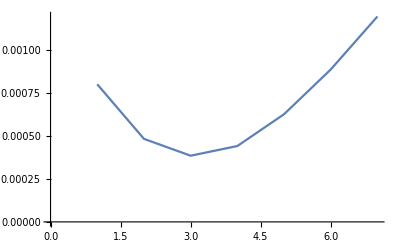

```mathematica
ListLinePlot[misfit8[0.5,1.5,0.0]]
```

```mathematica
d8=Table[misfit8[0.5,1.5,0],100]
ζ8=N[Mean[Table[Abs[3-Position[d8[[x]],Min[d8[[x]]]][[1,1]]]/3,{x,100}]]]
```

{{0.000455765,0.000250239,0.000250055,0.000375967,0.000609836,0.000902191,0.00123539},{0.000972622,0.000546941,0.000352694,0.000315443,0.00038067,0.000530409,0.000741422},{0.000648624,0.000366079,0.000271236,0.000314215,0.000471194,0.000692288,0.000962407},{0.00122393,0.00100098,0.000958556,0.00104289,0.0011922,0.00139517,0.00165286},{0.000755876,0.000503487,0.00044456,0.000525975,0.000687466,0.000913295,0.00119501},{0.000507775,0.000227534,0.000165162,0.000253451,0.000456243,0.000728061,0.00104436},{0.000534418,0.000255122,0.000149519,0.000183777,0.000319364,0.000522332,0.000777692},{0.000716687,0.000376857,0.000260283,0.000299176,0.000435334,0.000647697,0.000909115},{0.000690198,0.00034403,0.000206737,0.000209896,0.000323604,0.000508394,0.000743089},{0.000896471,0.00054879,0.000409056,0.000417461,0.000519512,0.00070008,0.000933946},{0.000685197,0.000371471,0.000250383,0.000272539,0.000385973,0.00057488,0.000816936},{0.000780449,0.000376412,0.000203548,0.000185504,0.00028083,0.000451135,0.000676638},{0.000636813,0.000395761,0.00034577,0.000427272,0.000598583,0.000830542,0.00110382},{0.000570104,0.00028216,0.000184859,0.000225838,0.000380709,0.000606832,0.00088058},{0.000637382,0.000314242,0.000191969,0.0002133,0.000330235,0.000514751,0.000756585},{0.000603127,0.000332752,0.000276965,0.000352737,0.000519744,0.000751506,0.00103312},{0.000674181,0.00035517,0.000244313,0.00027833,0.000432401,0.000656683,0.000925909},{0.000496105,0.000221241,0.000139372,0.000204067,0.000370733,0.000605612,0.00089497},{0.000818875,0.000469449,0.000326556,0.000323702,0.000419138,0.00059471,0.000832804},{0.000623132,0.000286802,0.000165835,0.000199265,0.000353556,0.000587008,0.000876189},{0.000726244,0.000416966,0.000310671,0.000354375,0.000490527,0.000701003,0.000971805},{0.000523557,0.000229093,0.000137663,0.000196546,0.000351688,0.000581435,0.000862531},{0.000675108,0.000408119,0.000325452,0.000386662,0.000560473,0.000802866,0.00109683},{0.000443585,0.000196971,0.000136287,0.000212919,0.000391299,0.00063493,0.000931628},{0.000401067,0.000178327,0.000152649,0.000260573,0.000468209,0.000737678,0.00104651},{0.00099584,0.000825741,0.000812495,0.000922702,0.00110691,0.00134218,0.00161895},{0.000350547,0.000173708,0.000175371,0.000311352,0.000536486,0.000821878,0.00114546},{0.000641226,0.00031579,0.000190239,0.000204608,0.000320869,0.000506081,0.000736465},{0.000586701,0.000302577,0.000215224,0.00026789,0.000420821,0.000646291,0.000916468},{0.000505282,0.000232475,0.00016152,0.000235814,0.000421272,0.000678167,0.000980747},{0.000439153,0.000268144,0.000267968,0.000385099,0.000589777,0.000847103,0.00114373},{0.000728636,0.00038886,0.000253936,0.000259173,0.000386727,0.000584858,0.00083512},{0.000959746,0.000571019,0.000417222,0.000423819,0.000545695,0.00074314,0.000986335},{0.0010508,0.000699697,0.000567261,0.000590391,0.000705316,0.000901348,0.00114897},{0.000689226,0.00038176,0.000257122,0.000277741,0.000395176,0.000586423,0.000839707},{0.000776205,0.000429002,0.000294268,0.000311399,0.000447464,0.000656889,0.000912358},{0.000913189,0.000510674,0.000318396,0.000297241,0.000389478,0.000571597,0.000813136},{0.000371388,0.000210619,0.000229784,0.000378112,0.000614921,0.000904839,0.00123683},{0.000567681,0.000272593,0.000173344,0.00021469,0.000367448,0.000584715,0.000847948},{0.000446622,0.000190539,0.000129333,0.000201428,0.000373643,0.00060826,0.000887224},{0.000747606,0.000417599,0.000315066,0.000356586,0.000522305,0.000760975,0.00104681},{0.000460021,0.000223413,0.000180351,0.000276732,0.00047958,0.000748709,0.00106108},{0.00110029,0.000934663,0.000921405,0.00103075,0.00120279,0.00142917,0.00170851},{0.000674816,0.000331137,0.000185303,0.000180895,0.000285189,0.000468891,0.000707652},{0.000569825,0.000260568,0.000161954,0.000206224,0.000357344,0.000579847,0.000851436},{0.00066685,0.000439097,0.000379069,0.000444656,0.000588524,0.000791669,0.0010468},{0.000521288,0.000248769,0.000165912,0.000222937,0.000383207,0.000607364,0.000881819},{0.000545408,0.000318926,0.000273679,0.00036847,0.000550463,0.000795291,0.00109047},{0.00046906,0.000262313,0.000224764,0.000313139,0.000489289,0.000727013,0.00100584},{0.00072835,0.000371605,0.00020345,0.000183586,0.000273906,0.000442663,0.000669717},{0.000369048,0.000196599,0.000203474,0.000343668,0.000577703,0.000870079,0.00120134},{0.000770731,0.000654293,0.000694524,0.000846693,0.00106328,0.00132397,0.00162168},{0.000342315,0.000209922,0.000245911,0.000398634,0.000635517,0.000920464,0.00124211},{0.000685745,0.000367017,0.000245315,0.00026629,0.000398122,0.000603577,0.0008588},{0.00048748,0.000224131,0.000160558,0.000234681,0.000421241,0.00067143,0.000966794},{0.000698746,0.00047117,0.000420218,0.000508023,0.000679268,0.000915796,0.0012065},{0.000642897,0.000581144,0.000668821,0.000870937,0.00113026,0.00143306,0.00177599},{0.000712843,0.000345302,0.000188482,0.000180374,0.000292216,0.000478097,0.000714897},{0.000482029,0.000205842,0.000128928,0.000194335,0.000363029,0.000595341,0.000874371},{0.000867248,0.000530359,0.000392305,0.000392335,0.000507614,0.000693317,0.00092565},{0.000359688,0.00015614,0.000139841,0.000253236,0.000469239,0.000746483,0.00106416},{0.000505135,0.000235769,0.000145899,0.000196291,0.000342598,0.000556368,0.000819026},{0.000487595,0.000251308,0.000199695,0.000276807,0.00045091,0.000684059,0.000965393},{0.000500068,0.000201765,0.0000954643,0.000136895,0.000284902,0.000507473,0.000779867},{0.000770337,0.000412337,0.000265593,0.000264032,0.000366323,0.00054158,0.0007732},{0.00036462,0.000180776,0.000178391,0.000307956,0.000519986,0.000790879,0.00111011},{0.000626865,0.000334516,0.000244923,0.000296819,0.000466109,0.000706545,0.00100072},{0.000931193,0.000544833,0.000383466,0.000366434,0.000478118,0.000665045,0.000898726},{0.000522408,0.00026927,0.000218576,0.000300712,0.000488643,0.000740376,0.00103993},{0.000635959,0.00031151,0.000189689,0.000214826,0.000336804,0.000533322,0.000781916},{0.00059278,0.000290851,0.000188875,0.000229491,0.000388333,0.000617586,0.000895678},{0.000356263,0.000193392,0.000200226,0.000333529,0.000550869,0.000823235,0.0011415},{0.000525345,0.000227712,0.000129227,0.000173674,0.000327472,0.000551535,0.000826721},{0.000581401,0.000318094,0.000245052,0.00030675,0.000451122,0.000662607,0.000926318},{0.000996022,0.000601898,0.000445801,0.000438703,0.000554506,0.000748241,0.000989387},{0.000545819,0.000297779,0.000234422,0.00030258,0.000463343,0.0006871,0.000955958},{0.000705827,0.000379935,0.000282154,0.000333386,0.000501275,0.000739529,0.00102147},{0.000753912,0.000355389,0.000177706,0.000150338,0.000242143,0.000410766,0.000640339},{0.000950128,0.000514938,0.000319198,0.000289059,0.00037218,0.000544528,0.000780381},{0.000654074,0.000602737,0.000697414,0.000909539,0.00118949,0.00151615,0.00187954},{0.000530506,0.000226254,0.000130552,0.000171631,0.000321544,0.000537131,0.000798398},{0.000720981,0.000367144,0.000236684,0.000249885,0.00037691,0.00057498,0.000823369},{0.000365637,0.00014692,0.000115329,0.000214036,0.000409551,0.000667411,0.000966595},{0.000481605,0.000266295,0.000245566,0.000355714,0.000556257,0.000814005,0.00111256},{0.000491438,0.000216863,0.000141179,0.000202573,0.00036786,0.000599273,0.000881654},{0.00072398,0.000366568,0.000206242,0.00018514,0.000271297,0.000431285,0.000645887},{0.000560903,0.000274803,0.000187748,0.000233864,0.000395448,0.000623325,0.000898136},{0.000860347,0.00042793,0.000223933,0.00017602,0.000253912,0.000413006,0.000632243},{0.00070224,0.000349209,0.000203504,0.000214646,0.000339136,0.000547595,0.000811694},{0.000578019,0.000250615,0.000124804,0.000141143,0.000266354,0.000462086,0.000705952},{0.00041394,0.000166266,0.00011247,0.000200455,0.000391832,0.000650572,0.000962169},{0.000501836,0.000209272,0.000117922,0.000172649,0.000339068,0.000579221,0.000868777},{0.000809336,0.00044412,0.000307438,0.000328724,0.000471542,0.000693139,0.000963537},{0.000998803,0.000710107,0.000592854,0.000617931,0.000727298,0.000901408,0.00113571},{0.000585054,0.000327171,0.000249297,0.000308723,0.000453404,0.000663798,0.000927242},{0.000517792,0.000230861,0.000138721,0.000196202,0.000355293,0.00058715,0.000875607},{0.000546527,0.00027164,0.000204627,0.000270266,0.000433299,0.000661559,0.000932424},{0.000558248,0.000268857,0.000177903,0.000227878,0.00038604,0.000615928,0.000902291},{0.000655216,0.000385223,0.000306837,0.000363453,0.000520004,0.000745135,0.00101167},{0.000431055,0.000253544,0.000271854,0.000421573,0.000660008,0.000956812,0.00129269}}

0.0766667